```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
xydata = Import["data.dat"];
```

```mathematica
(* Can separate the x and y parts; but Mathematica's plot function expects a 2D array *)
xdata = xydata[[;;,1]];
ydata = xydata[[;;,2]];
```

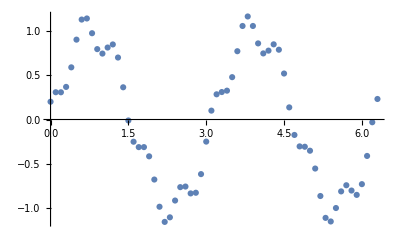

```mathematica
ListPlot[xydata]
```

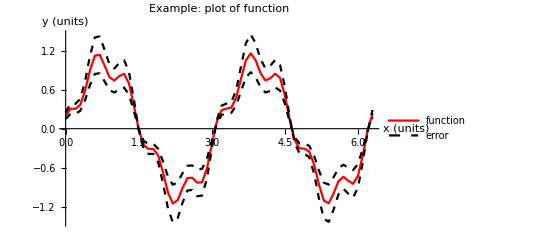

```mathematica
ListPlot[{xydata,
Transpose[{xdata,0.75*ydata}],
Transpose[{xdata,1.25*ydata}]},
Joined->True,
PlotStyle->{Red,{Black,Dashed},{Black,Dashed}},PlotLegends->{"function","error",None},
AxesLabel->{"x (units)","y (units)"},
PlotLabel->"Example: plot of function"]
```

...It can take a fair bit of work to make Mathematica plots look nice, but there is lot you can do